```mathematica
r1 = 118.5 ;
r2 = 121.5 ;
Δr = 5;
Δθ = 0.5 / 180 * π ;

detektor1 = {90, 180, 225, 135} ;
detektor2 = {296.81, 31.08, 55.91, 356.98} ;
σdetektor2 = {0.12, 0.17, 0.30, 0.12}   ;  (* niepewnosc statystyczna dofittowania*)

detektor1radians = detektor1 * π / 180  ;
detektor2radians = detektor2 * π / 180 ;
σdetektor2radians = {0.12, 0.17, 0.30, 0.12} * π / 180  ;  (* niepewnosc statystyczna dofittowania*)

x1 = r1* Cos[detektor1radians]  ;
y1 =  r1* Sin[detektor1radians]  ;

x2 = r2* Cos[detektor2radians] ;
y2 =  r2* Sin[detektor2radians] ;

σx2 = σdetektor2radians *r2* Abs [Sin[detektor2radians] ]  ;
σy2 = σdetektor2radians *r2* Abs[Cos[detektor2radians] ]  ;

Δx1 = Δr * Abs[Cos[detektor1radians]] + r1 * Abs[Sin[detektor1radians]]*Δθ ;
Δx2 = Δr * Abs[Cos[detektor2radians]] + r2 * Abs[Sin[detektor2radians]]*Δθ ;
Δy1 = Δr * Abs[Sin[detektor1radians]] + r1 * Abs[Cos[detektor1radians]]*Δθ ;
Δy2 = Δr * Abs[Sin[detektor2radians]] + r2 * Abs[Cos[detektor2radians]]*Δθ ;
```

```mathematica
(* Wyznaczanie współczynników korealcji liniowej *)

a = (y2 - y1) / (x2 - x1)  ;
b = (y1*x2 - y2*x1 ) / (x2 - x1) ;

σa = Sqrt[ ((-y1+y2)/(-x1+x2)^2)^2*σx2 ^ 2 + (1/(-x1+x2))^2 * σy2^2   ]  ;
σb = Sqrt[   ((x1 (-y1+y2))/(x1-x2)^2)^2  * σx2^2 + (x1/(-x1+x2))^2 * σy2^2] ;

Δa = Abs[ ((-y1+y2)/(-x1+x2)^2)] *Δx2  +Abs[ (1/(-x1+x2))]* Δy2  + Abs[((-y1+y2)/(-x1+x2)^2)] *Δx1  +Abs[ (1/(-x1+x2))]* Δy1 ;
Δb = Abs[((x1 (-y1+y2))/(x1-x2)^2)] * Δx2 + Abs[(x1/(-x1+x2))] * Δy2  + Abs[((x2 (-y1+y2))/(x1-x2)^2)] * Δx1 + Abs[(x2/(-x1+x2))] * Δy1          ;

a ;
σa;
b
σb
Δa
Δb
```

{118.5,33.3962,17.9405,46.9485}

{0.,0.166746,0.403991,0.103833}

{0.501476,0.0327716,0.122789,0.0472161}

{9.28244,3.72489,9.31279,5.08053}

```mathematica
line1[x_] := a[[1]] *x + b[[1]]
line2[x_] := a[[2]] *x + b[[2]]
line3[x_] := a[[3]] *x + b[[3]]
line4[x_] := a[[4]] *x + b[[4]]

xP = 19.242602722386263;
yP = 38.6343111061021;
```

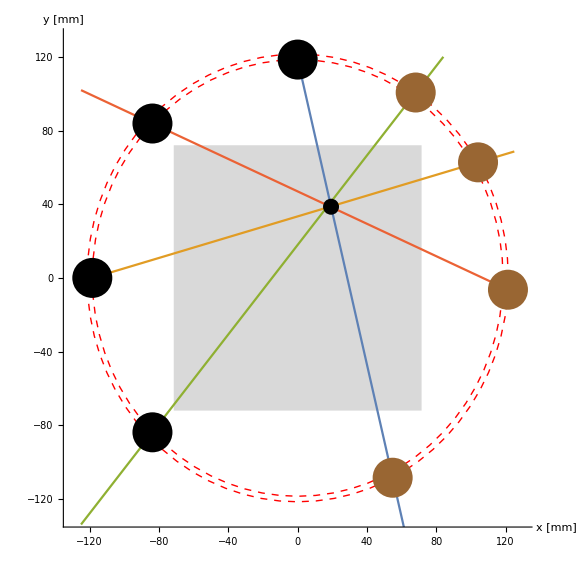

```mathematica
Show [
Graphics[ { Red,Dashed, Circle[{0,0}, 118.5] } ] ,
Graphics[ { Red,Dashed, Circle[{0,0}, 121.5] } ] ,
Graphics[ {LightGray,Rectangle[ {-71.5, -72}, {71.5, 72}  ]} ],

Plot[ {line1[x], line2[x], line3[x], line4[x]}, {x, -125, 125}, PlotRange->{{-150, 150}, {-150, 120}}], 

Graphics[{Black, PointSize[0.02],Point[ {xP, yP}] }],
Graphics[{Black, PointSize[0.05],Point[ {x1[[1]], y1[[1]]} ]}],
Graphics[{Black, PointSize[0.05],Point[ {x1[[2]], y1[[2]]} ]}],
Graphics[{Black, PointSize[0.05],Point[ {x1[[3]], y1[[3]]} ]}],
Graphics[{Black, PointSize[0.05],Point[ {x1[[4]], y1[[4]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[1]], y2[[1]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[2]], y2[[2]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[3]], y2[[3]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[4]], y2[[4]]} ]}],


Axes->True, AxesLabel->{"x [mm]", "y [mm]"}, AxesStyle->Black,
ImageSize->Large,
PlotRange-> {{-130, 130}, {-130,130}}

] (*end of the graphics*)
```

```mathematica
(* Wyznaczanie punkty przecięć *)

Solve[ {y == a[[1]]*x + b[[1]] , y == a[[2]]*x + b[[2]]} , {x,y}] ;
Solve[ {y == a[[2]]*x + b[[2]] , y == a[[4]]*x + b[[4]]} , {x,y}];
Solve[ {y == a[[4]]*x + b[[4]] , y == a[[3]]*x + b[[3]]} , {x,y}];
Solve[ {y == a[[1]]*x + b[[1]] , y == a[[3]]*x + b[[3]]} , {x,y}];

σxx1 = Sqrt[    ( σb[[1]]^2 + σb[[2]]^2)*(1 / a[[1]] - a[[2]])^2  +(σa[[1]]^2 +σa[[2]]^2) * (b[[1]]-b[[2]])^2 /( a[[1]] - a[[2]])^4  ];
σxx2 = Sqrt[    ( σb[[4]]^2 + σb[[2]]^2)*(1 / a[[4]] - a[[2]])^2  +(σa[[4]]^2 +σa[[2]]^2) * (b[[4]]-b[[2]])^2 /( a[[4]] - a[[2]])^4  ];
σxx3 = Sqrt[    ( σb[[3]]^2 + σb[[4]]^2)*(1 / a[[3]] - a[[4]])^2  +(σa[[3]]^2 +σa[[4]]^2) * (b[[3]]-b[[4]])^2 /( a[[3]] - a[[4]])^4  ];
σxx4 = Sqrt[    ( σb[[1]]^2 + σb[[3]]^2)*(1 / a[[1]] - a[[3]])^2  +(σa[[1]]^2 +σa[[3]]^2) * (b[[1]]-b[[3]])^2 /( a[[1]] - a[[3]])^4  ];

σyy1 = Sqrt[  ((a[[2]]* (b[[1]]- b[[2]]))/(a[[1]]-a[[2]])^2)^2 *( σa[[1]])^2 + ((a[[1]]* (b[[1]]- b[[2]]))/(a[[1]]-a[[2]])^2)^2 *( σa[[2]])^2  + (σb[[1]])^2 * (a[[2]] / (a[[1]]-a[[2]]))^2 + (σb[[2]])^2 * (a[[1]] / (a[[1]]-a[[2]]))^2  ] ;
σyy2 = Sqrt[  ((a[[2]]* (b[[4]]- b[[2]]))/(a[[4]]-a[[2]])^2)^2 *( σa[[4]])^2 + ((a[[4]]* (b[[4]]- b[[2]]))/(a[[4]]-a[[2]])^2)^2 *( σa[[2]])^2  + (σb[[4]])^2 * (a[[2]] / (a[[4]]-a[[2]]))^2 + (σb[[2]])^2 * (a[[4]] / (a[[4]]-a[[2]]))^2  ] ;
σyy3 = Sqrt[  ((a[[4]]* (b[[3]]- b[[4]]))/(a[[3]]-a[[4]])^2)^2 *( σa[[3]])^2 + ((a[[3]]* (b[[3]]- b[[4]]))/(a[[3]]-a[[4]])^2)^2 *( σa[[4]])^2  + (σb[[3]])^2 * (a[[4]] / (a[[3]]-a[[4]]))^2 + (σb[[4]])^2 * (a[[3]] / (a[[3]]-a[[4]]))^2  ] ;
σyy4 = Sqrt[  ((a[[3]]* (b[[1]]- b[[3]]))/(a[[1]]-a[[3]])^2)^2 *( σa[[1]])^2 + ((a[[1]]* (b[[1]]- b[[3]]))/(a[[1]]-a[[3]])^2)^2 *( σa[[3]])^2  + (σb[[1]])^2 * (a[[3]] / (a[[1]]-a[[3]]))^2 + (σb[[3]])^2 * (a[[1]] / (a[[1]]-a[[3]]))^2  ] ;


Δxx1 =  ( Δb[[1]] + Δb[[2]] )*Abs[(1 / a[[1]] - a[[2]]) ] +( Δa[[1]] +Δa[[2]]) * Abs[( b[[1]]-b[[2]]) /( a[[1]] - a[[2]])^2  ];
Δxx2 =  ( Δb[[4]] + Δb[[2]] )*Abs[(1 / a[[4]] - a[[2]]) ] +( Δa[[4]] +Δa[[2]]) * Abs[( b[[4]]-b[[2]]) /( a[[4]] - a[[2]])^2  ];
Δxx3 =  ( Δb[[4]] + Δb[[3]] )*Abs[(1 / a[[4]] - a[[3]]) ] +( Δa[[4]] +Δa[[3]]) * Abs[( b[[4]]-b[[3]]) /( a[[4]] - a[[3]])^2  ];
Δxx4 =  ( Δb[[1]] + Δb[[3]] )*Abs[(1 / a[[1]] - a[[3]]) ] +( Δa[[1]] +Δa[[3]]) * Abs[( b[[1]]-b[[3]]) /( a[[1]] - a[[3]])^2  ];

Δyy1 = Abs[  ((a[[2]]* (b[[1]]- b[[2]]))/(a[[1]]-a[[2]])^2)] *Δa[[1]]+Abs[((a[[1]]* (b[[1]]- b[[2]]))/(a[[1]]-a[[2]])^2)] *( Δa[[2]])+(Δb[[1]])* Abs[(a[[2]] / (a[[1]]-a[[2]]))] + (Δb[[2]]) * Abs[(a[[1]] / (a[[1]]-a[[2]]))  ] ;
Δyy2 = Abs[  ((a[[2]]* (b[[4]]- b[[2]]))/(a[[4]]-a[[2]])^2)] *Δa[[4]]+Abs[((a[[4]]* (b[[4]]- b[[2]]))/(a[[4]]-a[[2]])^2)] *( Δa[[2]])+(Δb[[4]])* Abs[(a[[2]] / (a[[4]]-a[[2]]))] + (Δb[[2]]) * Abs[(a[[4]] / (a[[4]]-a[[2]]))  ] ;

Δyy3 = Abs[  ((a[[3]]* (b[[4]]- b[[3]]))/(a[[4]]-a[[3]])^2)] *Δa[[4]]+Abs[((a[[4]]* (b[[4]]- b[[3]]))/(a[[4]]-a[[3]])^2)] *( Δa[[3]])+(Δb[[4]])* Abs[(a[[3]] / (a[[4]]-a[[3]]))] + (Δb[[3]]) * Abs[(a[[4]] / (a[[4]]-a[[3]]))  ] ;

Δyy4 = Abs[  ((a[[3]]* (b[[1]]- b[[3]]))/(a[[1]]-a[[3]])^2)] *Δa[[1]]+Abs[((a[[1]]* (b[[1]]- b[[3]]))/(a[[1]]-a[[3]])^2)] *( Δa[[3]])+(Δb[[1]])* Abs[(a[[3]] / (a[[1]]-a[[3]]))] + (Δb[[3]]) * Abs[(a[[1]] / (a[[1]]-a[[3]]))  ] ;



xx = {19.24110776484659, 18.7827422866855, 17.540144228868236, 18.77757694933716}
yy= {38.81887078800059, 38.68969199338255, 39.23606574975086, 40.73844107759847}

σxx = {σxx1, σxx2, σxx3, σxx4} 
σyy = {σyy1, σyy2, σyy3, σyy4} 

Δxx = {Δxx1,Δxx2,Δxx3,Δxx4}
Δyy = {Δyy1,Δyy2,Δyy3,Δyy4}
```

{19.2411,18.7827,17.5401,18.7776}

{38.8189,38.6897,39.2361,40.7384}

{0.115364,0.504464,0.52961,0.591401}

{0.15958,0.110963,0.134565,0.328502}

{9.13085,24.5897,52.0123,29.2558}

{5.2842,4.97591,7.38638,13.2237}

```mathematica
(* Wyznaczenie punktów o minimalnej odległości *)
xIntSec = {19.24110776484659, 18.7827422866855, 17.540144228868236, 18.77757694933716} ;
yIntSec = {38.81887078800059, 38.68969199338255,  39.23606574975086,  40.73844107759847} ;

ttx = Total[(xIntSec - x0 )^2] +  Total[(yIntSec - y0 )^2] ;

solution=NMinimize[ttx,{x0,y0}]
```

{4.25552,{x0→18.5854,y0→39.3708}}

```mathematica
experiment=Sum[z[i]{xIntSec[[i]],yIntSec[[i]]},{i,1,4}];
exptotal = Total[Table[Norm[experiment-{xIntSec[[i]],yIntSec[[i]]}]^2,{i,1,4}]]
Minimize[exptotal,{z[1],z[2],z[3],z[4]}]
```

Abs[-19.2411+19.2411 z[1]+18.7827 z[2]+17.5401 z[3]+18.7776 z[4]]^2+Abs[-18.7827+19.2411 z[1]+18.7827 z[2]+17.5401 z[3]+18.7776 z[4]]^2+Abs[-18.7776+19.2411 z[1]+18.7827 z[2]+17.5401 z[3]+18.7776 z[4]]^2+Abs[-17.5401+19.2411 z[1]+18.7827 z[2]+17.5401 z[3]+18.7776 z[4]]^2+Abs[-40.7384+38.8189 z[1]+38.6897 z[2]+39.2361 z[3]+40.7384 z[4]]^2+Abs[-39.2361+38.8189 z[1]+38.6897 z[2]+39.2361 z[3]+40.7384 z[4]]^2+Abs[-38.8189+38.8189 z[1]+38.6897 z[2]+39.2361 z[3]+40.7384 z[4]]^2+Abs[-38.6897+38.8189 z[1]+38.6897 z[2]+39.2361 z[3]+40.7384 z[4]]^2

{4.25552,{z[1]→0.368203,z[2]→0.262777,z[3]→0.564726,z[4]→-0.177888}}

```mathematica
P =  {x0,y0}/.solution[[2]]
xP = P[[1]]
yP = P[[2]]
```

{18.5854,39.3708}

18.5854

39.3708

```mathematica
weight = {0.3682033743880332,0.2627771964494072, 0.5647262007575624,-0.1778878807640611}
XP = Total[xx*weight]
YP  = Total[yy*weight]
σXP = Total[σxx*weight]
σYP = Total[σyy*weight]
ΔXP = Total[Δxx*weight]
ΔYP = Total[Δyy*weight]
```

{0.368203,0.262777,0.564726,-0.177888}

18.5854

39.3708

0.368921

0.105472

33.9921

5.07216

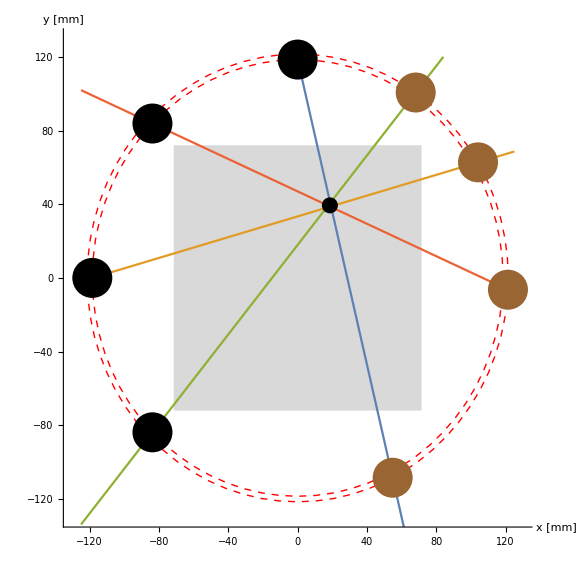

```mathematica
Show [
Graphics[ { Red,Dashed, Circle[{0,0}, 118.5] } ] ,
Graphics[ { Red,Dashed, Circle[{0,0}, 121.5] } ] ,
Graphics[ {LightGray,Rectangle[ {-71.5, -72}, {71.5, 72}  ]} ],

Plot[ {line1[x], line2[x], line3[x], line4[x]}, {x, -125, 125}, PlotRange->{{-150, 150}, {-150, 120}}], 

Graphics[{Black, PointSize[0.02],Point[ {xP, yP}] }],
Graphics[{Black, PointSize[0.05],Point[ {x1[[1]], y1[[1]]} ]}],
Graphics[{Black, PointSize[0.05],Point[ {x1[[2]], y1[[2]]} ]}],
Graphics[{Black, PointSize[0.05],Point[ {x1[[3]], y1[[3]]} ]}],
Graphics[{Black, PointSize[0.05],Point[ {x1[[4]], y1[[4]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[1]], y2[[1]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[2]], y2[[2]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[3]], y2[[3]]} ]}],
Graphics[{Brown, PointSize[0.05],Point[ {x2[[4]], y2[[4]]} ]}],


Axes->True, AxesLabel->{"x [mm]", "y [mm]"}, AxesStyle->Black,
ImageSize->Large,
PlotRange-> {{-130, 130}, {-130,130}}

] (*end of the graphics*)
```

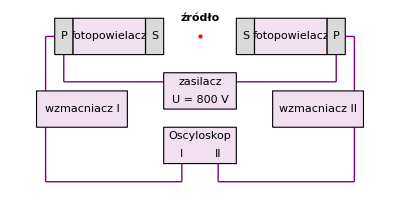

```mathematica
Show[
Graphics[ {PointSize[Large],Text[ Style["źródło", Medium, Bold], {5,9}],Red, Point[{5,8.5}]}] , 

Graphics[ {Purple,Thick, Line[{{0.75,4.5},{0.75,8.5}}], Line[{{0.75,8.5}, {1.5, 8.5} }]  }],

Graphics[ {Purple,Thick, Line[{{9.25,4.5},{9.25,8.5}}], Line[{{8.5,8.5}, {9.25, 8.5} }]  }],

Graphics[ {Purple,Thick, Line[{{1.25,7.25},{8.75,7.25}}], Line[{{1.25,7.25}, {1.25, 8} }], Line[{{8.75,7.25}, {8.75, 8} }]  }],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{4,6.5},{6,7.5}],
 Black, Text["zasilacz",{5,7.25}],
 Black, Text["U = 800 V",{5,6.75}]
  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{0.5,6},{3,7}],
 Black, Text["wzmacniacz I",{1.75,6.5}]
  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{7,6},{9.5,7}],
 Black, Text["wzmacniacz II",{8.25,6.5}]
  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{1.5,8},{3.5,9}],
LightGray,Rectangle[{1,8}, {1.5,9}], Black, Text[P,{1.25,8.5}],
LightGray,Rectangle[{3.5,8}, {4,9}], Black, Text[S,{3.75,8.5}],
Black,Text["fotopowielacz", {2.5,8.5}]  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{6.5,8},{8.5,9}],
LightGray,Rectangle[{6,8}, {6.5,9}], Black, Text[S,{6.25,8.5}],
LightGray,Rectangle[{8.5,8}, {9,9}], Black, Text[P,{8.75,8.5}],
Black,Text["fotopowielacz" , {7.5,8.5}]  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{4,5},{6,6}],
 Black, Text["Oscyloskop",{5,5.75}],
  Text["I",{4.5,5.25}],   Text["II",{5.5,5.25}]
  } ],
Graphics[ {Purple,Thick, Line[{{0.75,4.5},{4.5,4.5}}], Line[{{5.5,4.5},{9.25,4.5}}], Line[{{4.5,4.5}, {4.5, 5} }],  Line[{{5.5,4.5}, {5.5, 5} }]  }]
]
```

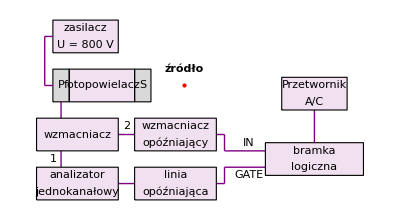

```mathematica
Show[

Graphics[ {PointSize[Large],Text[ Style["źródło", Medium, Bold], {5,9}],Red, Point[{5,8.5}]}] , 

Graphics[ {Purple,Thick, Line[{{1.25,6},{1.25,8}}], Line[{{2.5,7}, {4,7} }],  Line[{{2.5,5.5}, {4,5.5} }], 
 Line[{{9, 6.5}, {9,8} }], 
Line[{{6, 5.5}, {6.25,5.5} }],Line[{{6.25, 5.5}, {6.25, 6} }],  Line[{{6.25, 6}, {7.5, 6} }],
Line[{{6, 7}, {6.25,7} }],Line[{{6.25, 7}, {6.25, 6.5} }],  Line[{{6.25, 6.5}, {7.5, 6.5} }]
  }],
Graphics[{LightPurple,EdgeForm[Black],Rectangle[{1,9.5},{3,10.5}],
 Black, Text["zasilacz",{2,10.25}],
 Black, Text["U = 800 V",{2,9.75}]
  } ], 

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{1.5,8},{3.5,9}],
LightGray,Rectangle[{1,8}, {1.5,9}], Black, Text[P,{1.25,8.5}],
LightGray,Rectangle[{3.5,8}, {4,9}], Black, Text[S,{3.75,8.5}],
Black,Text["fotopowielacz", {2.5,8.5}]  } ], 

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{0.5,6.5},{3,7.5}],
 Black, Text["wzmacniacz ",{1.75,7}]
  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{0.5,5},{3,6}],
 Black, Text["analizator",{1.75,5.75}],
 Black, Text["jednokanałowy",{1.75,5.25}]
  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{3.5,5},{6,6}],
 Black, Text["linia",{4.75,5.75}],
 Black, Text["opóźniająca",{4.75,5.25}]
  } ],

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{3.5,6.5},{6,7.5}],
 Black, Text["wzmacniacz",{4.75,7.25}],
 Black, Text["opóźniający",{4.75,6.75}]
  } ] ,

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{7.5,5.75},{10.5,6.75}],
 Black, Text["bramka",{9,6.5}],
 Black, Text["logiczna",{9,6}]
  } ] ,

Graphics[{LightPurple,EdgeForm[Black],Rectangle[{8,7.75},{10,8.75}],
 Black, Text["Przetwornik",{9,8.5}],
 Black, Text["A/C",{9,8}]
  } ] ,

Graphics[ {Purple,Thick, Line[{{0.75,8.5},{0.75,10}}], Line[{{0.75,8.5}, {1, 8.5} }], Line[{{0.75,10}, {1, 10} }]  }],

Graphics[ { Black, Thick, Text["IN", {7, 6.75}],  Text["GATE", {7, 5.75}],  Text["1", {1, 6.25}],  Text["2", {3.25, 7.25}]   }]

]
```